```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\John K\Dropbox\Mathematica Notebooks\DropletRNBcalib

```mathematica
numberLabels=StringPartition["000102030405101112131415202122232425303132333435404142434445505152535455",2];
cosNumberLabels="c"<>#&/@numberLabels;
sinNumberLabels="s"<>#&/@numberLabels;
tanNumberLabels="t"<>#&/@numberLabels;
```

```mathematica
test=Import["resultsNCexpanded.csv",HeaderLines->1];
```

```mathematica
Dimensions[test]
```

{2559,151}

```mathematica
SemanticImport["ExampleData/RetailSales.tsv"]
```

SemanticImport::unexpinvaliderr: Unexpected invalid input was detected.  Processing will not continue

$Failed

```mathematica
$TemporaryDirectory
```

C:\Users\John K\AppData\Local\Temp

```mathematica
Block[{$TemporaryDirectory="C:\\tmp\\"},dat=SemanticImport["resultsExpanded.csv"]; datNC=SemanticImport["resultsNCExpanded.csv"];];
```

```mathematica
dat=SemanticImport["resultsExpanded.csv"];
datNC=SemanticImport["resultsNCexpanded.csv"];
```

SemanticImport::unexpinvaliderr: Unexpected invalid input was detected.  Processing will not continue

```mathematica
datForPredictX=(numberLabels->"RBx")/.Normal[dat];
datForPredictY=(numberLabels->"RBy")/.Normal[dat];
datForPredictNCx=(numberLabels->"RBx")/.Normal[datNC];
datForPredictNCy=(numberLabels->"RBy")/.Normal[datNC];
```

ColumnForm::colmh: Horizontal alignment specification ImageSize→400 is not Left, Center, or Right.

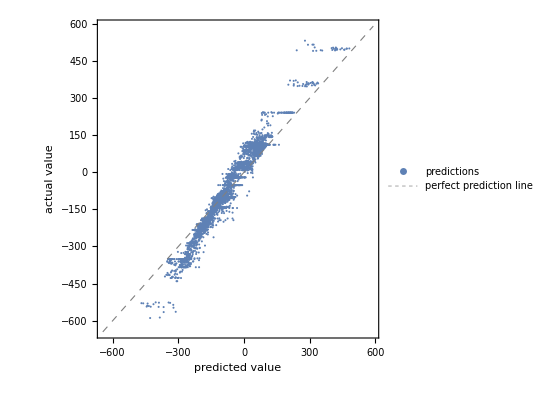
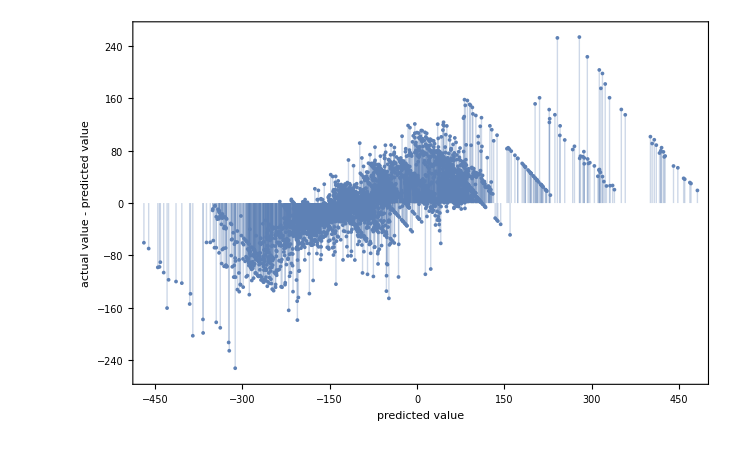

```mathematica
pX=Predict[datForPredictX,PerformanceGoal->"Quality"];
pmX=PredictorMeasurements[pX,datForPredictX];
ColumnForm[{pmX["ComparisonPlot"],pmX["ResidualPlot"]},ImageSize->400]
```

ColumnForm::colmh: Horizontal alignment specification ImageSize→400 is not Left, Center, or Right.

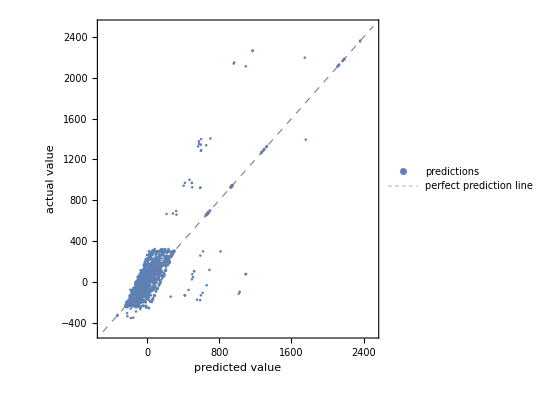
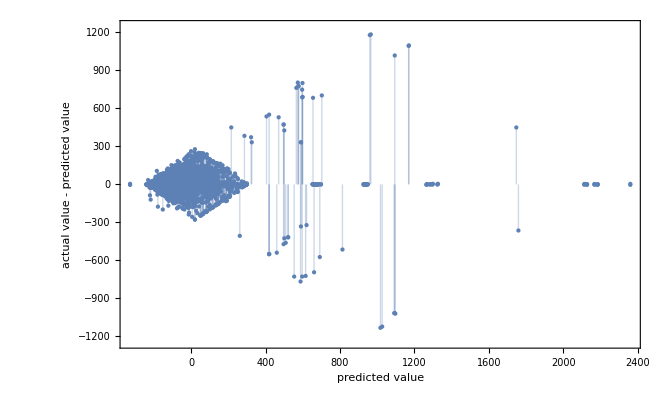

```mathematica
pY=Predict[datForPredictY,PerformanceGoal->"Quality"];
pmY=PredictorMeasurements[pY,datForPredictY];
ColumnForm[{pmY["ComparisonPlot"],pmY["ResidualPlot"]},ImageSize->400]
```

```mathematica
(#->PredictorInformation[pNCx,#]&)/@Select[PredictorInformation[pNCx,"Properties"],#≠"Properties"&]
```

{ExampleNumber→2559,ExtractedFeatureNumber→36,FeatureNumber→1,FunctionProperties→{Decision,Distribution,Properties,Votes},LeafSize→5,MaxTrainingMemory→20165728 B,MethodDescription→The random forest predictor uses an ensemble of decision trees to predict the value. Each decision tree has been trained on a random subset of the training set, and only uses a random subset of the features.,TrainingTime→40.3571 s,TreeNumber→200}

```mathematica
(#->PredictorInformation[pNCy,#]&)/@Select[PredictorInformation[pNCx,"Properties"],#≠"Properties"&]
```

{ExampleNumber→2559,ExtractedFeatureNumber→36,FeatureNumber→1,FunctionProperties→{Decision,Distribution,Properties,Votes},LeafSize→5,MaxTrainingMemory→20127368 B,MethodDescription→The random forest predictor uses an ensemble of decision trees to predict the value. Each decision tree has been trained on a random subset of the training set, and only uses a random subset of the features.,TrainingTime→42.5055 s,TreeNumber→200}

ColumnForm::colmh: Horizontal alignment specification ImageSize→400 is not Left, Center, or Right.

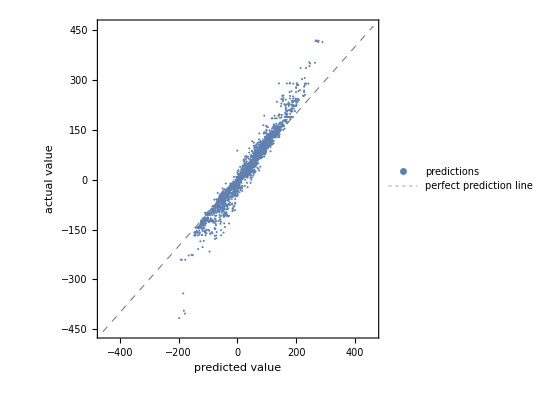
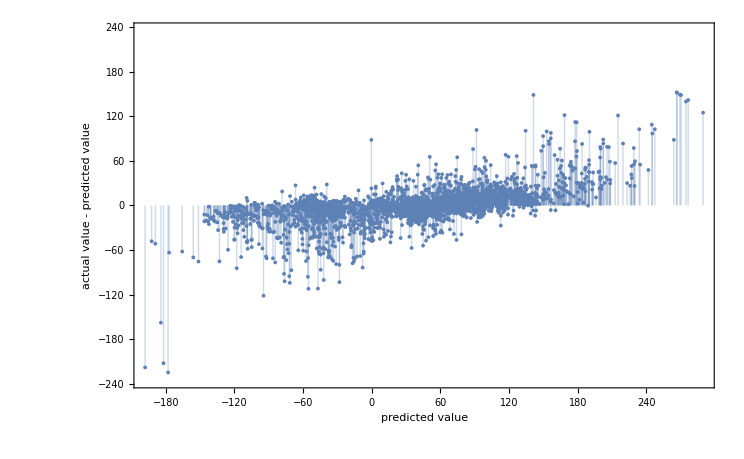

```mathematica
pNCx=Predict[datForPredictNCx,PerformanceGoal->"Quality"];
pmNCx=PredictorMeasurements[pNCx,datForPredictNCx];
ColumnForm[{pmNCx["ComparisonPlot"],pmNCx["ResidualPlot"]},ImageSize->400]
```

ColumnForm::colmh: Horizontal alignment specification ImageSize→400 is not Left, Center, or Right.

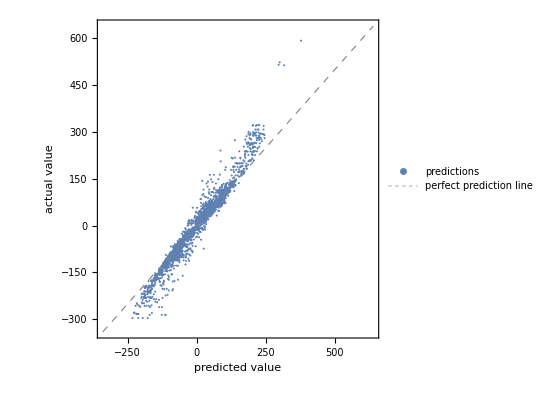
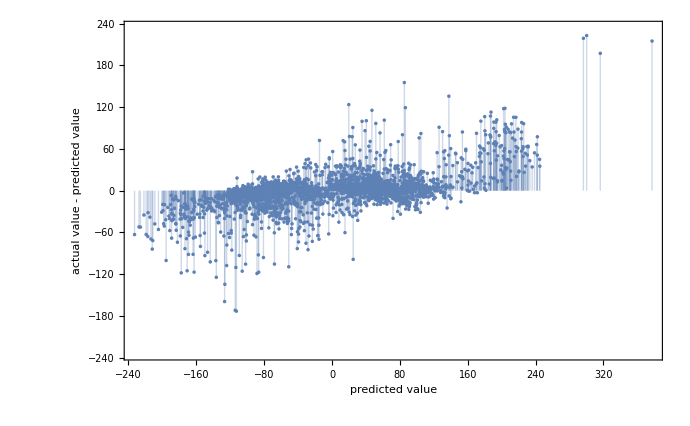

```mathematica
pNCy=Predict[datForPredictNCy,PerformanceGoal->"Quality"];
pmNCy=PredictorMeasurements[pNCy,datForPredictNCy];
ColumnForm[{pmNCy["ComparisonPlot"],pmNCy["ResidualPlot"]},ImageSize->400]
```

ColumnForm::colmh: Horizontal alignment specification ImageSize→400 is not Left, Center, or Right.

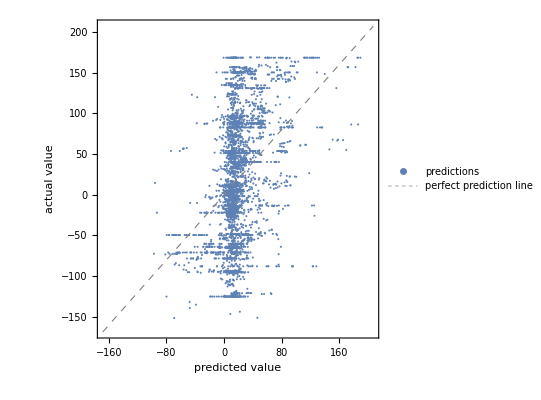
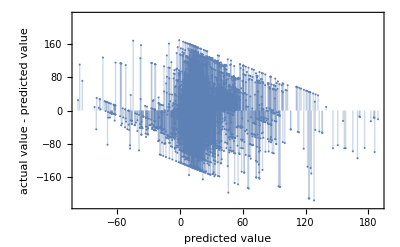

```mathematica
pX=Predict[datForPredictX,PerformanceGoal->{"Quality","Memory"}];
pmX=PredictorMeasurements[pX,datForPredictX];
ColumnForm[{pmX["ComparisonPlot"],pmX["ResidualPlot"]},ImageSize->400]
```

ColumnForm::colmh: Horizontal alignment specification ImageSize→400 is not Left, Center, or Right.

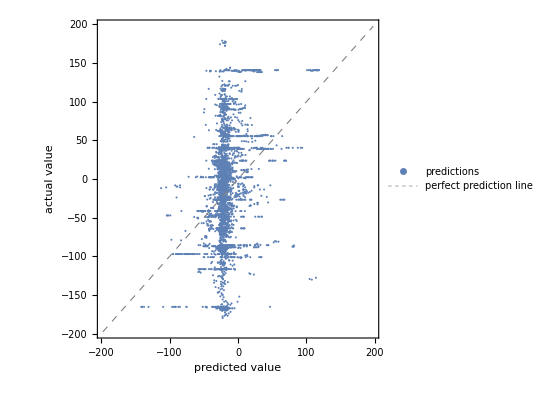
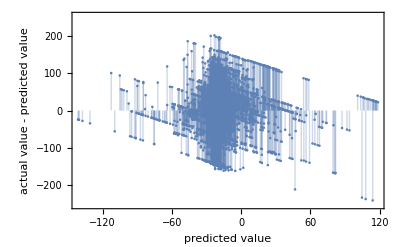

```mathematica
pY=Predict[datForPredictY,PerformanceGoal->{"Quality","Memory"}];
pmY=PredictorMeasurements[pY,datForPredictY];
ColumnForm[{pmY["ComparisonPlot"],pmY["ResidualPlot"]},ImageSize->400]
```

ColumnForm::colmh: Horizontal alignment specification ImageSize→400 is not Left, Center, or Right.

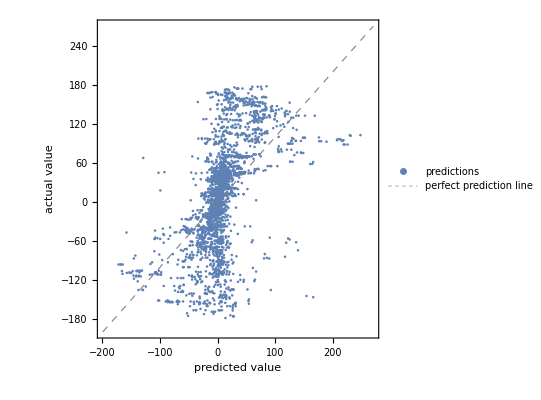
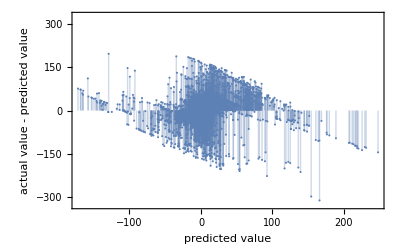

```mathematica
pNCx=Predict[datForPredictNCx,PerformanceGoal->{"Quality","Memory"}];
pmNCx=PredictorMeasurements[pNCx,datForPredictNCx];
ColumnForm[{pmNCx["ComparisonPlot"],pmNCx["ResidualPlot"]},ImageSize->400]
```

ColumnForm::colmh: Horizontal alignment specification ImageSize→400 is not Left, Center, or Right.

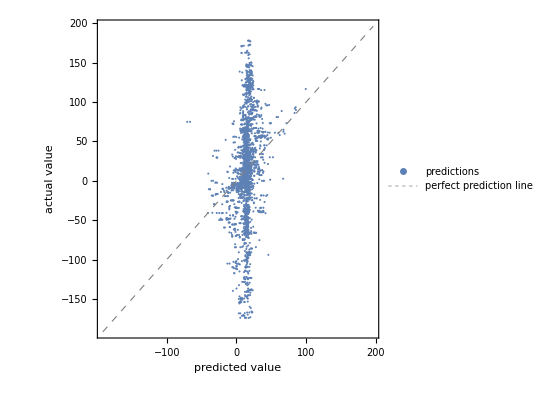
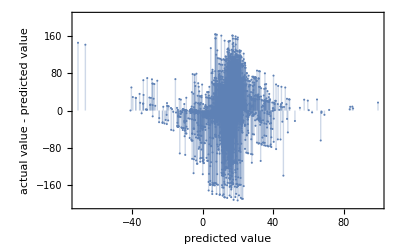

```mathematica
pNCy=Predict[datForPredictNCy,PerformanceGoal->{"Quality","Memory"}];
pmNCy=PredictorMeasurements[pNCy,datForPredictNCy];
ColumnForm[{pmNCy["ComparisonPlot"],pmNCy["ResidualPlot"]},ImageSize->400]
```